{{x→2}}

0

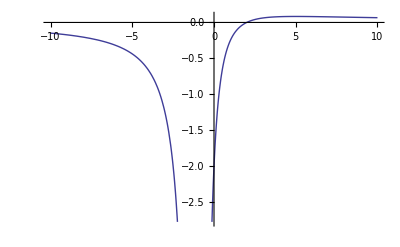

(x-2)/(x+1)^2

```mathematica
f[x_]:=(x-2)/(x+1)^2
Solve[f[x]==0, {x}]
Limit[f[x ], x-> Infinity]
Plot[f[x], {x, -10, 10}]
```

```mathematica
Solve[x^2+2x+5==0, {x}]
```

{{x→-1-2 ⅈ},{x→-1+2 ⅈ}}

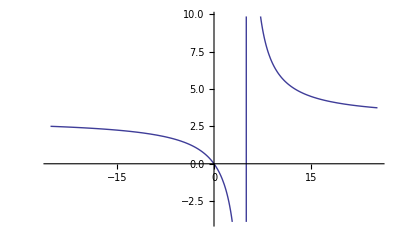

```mathematica
Plot[(3 x)/(-5+x),{x,-25.25,25.25}]
```

```mathematica
Clear[f,x]
```

```mathematica
ClearAll
```

```mathematica
f[x]
```

(3 x)/(-5+x)

```mathematica
Plot[(3 x)/(-5+x),{x,-25.25,25.25}]
```

-Graphics-

```mathematica
Solve[f[x]==0,{x}]
```

{{x→1}}

```mathematica
f[x]
```

(-1+x)/(4+x)

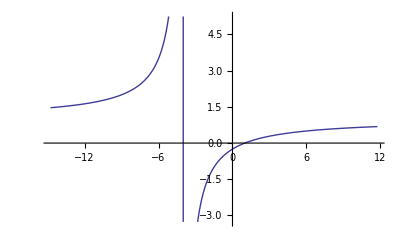

```mathematica
Plot[(-1+x)/(4+x),{x,-14.759999999999998,11.759999999999998}]
```

```mathematica
6/711//N
```

0.00843882

```mathematica
177/711//N
```

0.248945

x intercept

{{x→0},{x→-ⅈ},{x→ⅈ}}

y intercept

0

vertical asymptote

{{x→-1},{x→1}}

slant asymptote

2 x

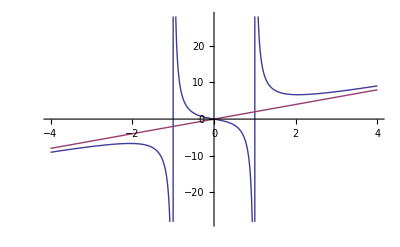

```mathematica
n[x_]:=2x^3+2x;
d[x_]:=x^2-1;
g[x_]:=n[x]/d[x];

Print["x intercept"]
xIntercept=Solve[n[x]==0,{x}]

Print["y intercept"]
 g[0]

Print["vertical asymptote"]
vertical=Solve[d[x]==0,{x}]

(*
Print["horizontal asymptote"]
horizontal = Limit[g[x],{x->Infinity}]
*)
Print["slant asymptote"]
slant = PolynomialQuotient[n[x],d[x],x]

Plot[{g[x],slant}, {x, -4,4}]
```

```mathematica
Solve[x^3+4==0,{x}]
```

{{x→-(-2)^(2/3)},{x→-2^(2/3)},{x→(-1)^(1/3) 2^(2/3)}}

```mathematica
{{x->-(-2)^(2/3)},{x->-2^(2/3)},{x->(-1)^(1/3) 2^(2/3)}}/.Rule->List
```

{{{x,-(-2)^(2/3)}},{{x,-2^(2/3)}},{{x,(-1)^(1/3) 2^(2/3)}}}

```mathematica
(-4)^(1/3)//Expand//TraditionalForm
```

-1^(1/3) 2^(2/3)

x x

{-3,14-12 x}

x

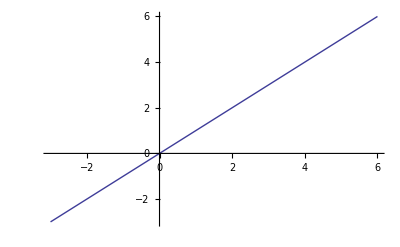

```mathematica
g=x
g//TraditionalForm
PolynomialQuotientRemainder[2-3x^2,x^2-4x+4,x]
g//Factor
Plot[g,{x,-3,6}]
```

```mathematica
ClearAll[f]
```

(2 x^2+4 x+5)/(x^2+2 x+1)

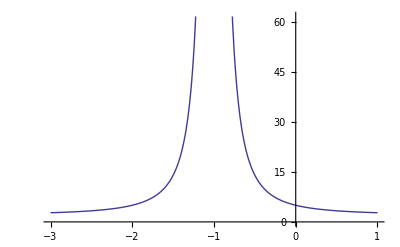

```mathematica
f=(2x^2+4x+5)/(x^2+2x+1);
f//TraditionalForm
Plot[f, {x,-3,1}]
```

```mathematica
2 + 3/(x+1)^2//Together
```

(5+4 x+2 x^2)/(1+x)^2